# HypergraphRewriting Paclet Examples

This notebook demonstrates the HGEvolve function for high-performance hypergraph rewriting and multiway evolution.

## Installation and Setup

First, load the paclet from its directory. The library must be built for your platform (see README.md for build instructions).

```mathematica
(* Load the paclet from its directory *)
PacletDirectoryLoad[pacletDir]
```

```mathematica
<<HypergraphRewriting`
```

HypergraphRewriting: Library functions loaded successfully

## Basic Multiway Evolution

The core function is HGEvolve, which performs multiway rewriting.

### Simple Binary Splitting

```mathematica
(* Define a rule that splits binary edges *)
rules = {{{1, 2}} -> {{1, 3}, {3, 2}}};
initialEdges = {{1, 2}};

(* Evolve for 3 steps *)
HGEvolve[rules, initialEdges, 3]
```

-Graphics-

### Ternary to Binary Rule

```mathematica
(* Classic Wolfram Physics rule *)
rules = {{{1, 2, 3}} -> {{1, 2}, {2, 3}, {3, 1}}};
initialEdges = {{1, 2, 3}};

HGEvolve[rules, initialEdges, 3, "StatesGraph"]
```

-Graphics-

## Extracting Properties

HGEvolve returns different data based on the property argument.

### Getting States and Events

```mathematica
(* Define rules *)
rules = {{{1,2},{2,3}} -> {{1,2},{2,3},{3,4}}};
initialEdges = {{1,1},{1,1}};

(* Get the states *)
states = HGEvolve[rules, initialEdges, 2, "States"]
```

<|10→{{5,1,1},{29,1,1},{30,1,3},{31,3,11}},9→{{7,1,3},{26,1,1},{27,1,1},{28,1,10}},8→{{6,1,1},{23,1,1},{24,1,3},{25,3,9}},7→{{3,1,1},{20,1,1},{21,1,2},{22,2,8}},6→{{4,1,2},{17,1,1},{18,1,1},{19,1,7}},5→{{2,1,1},{14,1,1},{15,1,2},{16,2,6}},4→{{7,1,3},{11,1,1},{12,1,1},{13,1,5}},3→{{4,1,2},{8,1,1},{9,1,1},{10,1,4}},2→{{5,1,1},{6,1,1},{7,1,3}},1→{{2,1,1},{3,1,1},{4,1,2}},0→{{0,1,1},{1,1,1}}|>

```mathematica
(* Get the events *)
events = HGEvolve[rules, initialEdges, 2, "Events"]
```

<|0→<|EventId→0,RuleIndex→0,Multiplicity→1,InputStateId→0,OutputStateId→1,CanonicalInputStateId→0,CanonicalOutputStateId→1,ConsumedEdges→{1,0},ProducedEdges→{2,3,4}|>,1→<|EventId→1,RuleIndex→0,Multiplicity→1,InputStateId→0,OutputStateId→2,CanonicalInputStateId→0,CanonicalOutputStateId→1,ConsumedEdges→{0,1},ProducedEdges→{5,6,7}|>,2→<|EventId→2,RuleIndex→0,Multiplicity→1,InputStateId→1,OutputStateId→3,CanonicalInputStateId→1,CanonicalOutputStateId→3,ConsumedEdges→{2,4},ProducedEdges→{8,9,10}|>,3→<|EventId→3,RuleIndex→0,Multiplicity→1,InputStateId→1,OutputStateId→4,CanonicalInputStateId→1,CanonicalOutputStateId→4,ConsumedEdges→{2,3},ProducedEdges→{11,12,13}|>,4→<|EventId→4,RuleIndex→0,Multiplicity→1,InputStateId→1,OutputStateId→5,CanonicalInputStateId→1,CanonicalOutputStateId→4,ConsumedEdges→{3,2},ProducedEdges→{14,15,16}|>,5→<|EventId→5,RuleIndex→0,Multiplicity→1,InputStateId→2,OutputStateId→6,CanonicalInputStateId→1,CanonicalOutputStateId→3,ConsumedEdges→{5,7},ProducedEdges→{17,18,19}|>,6→<|EventId→6,RuleIndex→0,Multiplicity→1,InputStateId→2,OutputStateId→8,CanonicalInputStateId→1,CanonicalOutputStateId→4,ConsumedEdges→{6,5},ProducedEdges→{23,24,25}|>,7→<|EventId→7,RuleIndex→0,Multiplicity→1,InputStateId→2,OutputStateId→9,CanonicalInputStateId→1,CanonicalOutputStateId→3,ConsumedEdges→{6,7},ProducedEdges→{26,27,28}|>,8→<|EventId→8,RuleIndex→0,Multiplicity→1,InputStateId→2,OutputStateId→7,CanonicalInputStateId→1,CanonicalOutputStateId→4,ConsumedEdges→{5,6},ProducedEdges→{20,21,22}|>,9→<|EventId→9,RuleIndex→0,Multiplicity→1,InputStateId→1,OutputStateId→10,CanonicalInputStateId→1,CanonicalOutputStateId→3,ConsumedEdges→{3,4},ProducedEdges→{29,30,31}|>|>

```mathematica
(* Get counts *)
Print["Number of states: ", HGEvolve[rules, initialEdges, 2, "NumStates"]];
Print["Number of events: ", HGEvolve[rules, initialEdges, 2, "NumEvents"]]
```

Number of states: 4

Number of events: 10

### Causal and Branchial Edges

```mathematica
(* Get causal relationships *)
causalEdges = HGEvolve[rules, initialEdges, 2, "CausalEdges"]
```

{<|From→0,To→5,Multiplicity→1|>,<|From→0,To→6,Multiplicity→1|>,<|From→0,To→7,Multiplicity→1|>,<|From→0,To→9,Multiplicity→1|>,<|From→1,To→2,Multiplicity→1|>,<|From→1,To→3,Multiplicity→1|>,<|From→1,To→4,Multiplicity→1|>,<|From→1,To→8,Multiplicity→1|>}

```mathematica
(* Get branchial relationships *)
branchialEdges = HGEvolve[rules, initialEdges, 2, "BranchialEdges"]
```

{<|From→0,To→1,Multiplicity→1|>,<|From→2,To→4,Multiplicity→1|>,<|From→2,To→5,Multiplicity→1|>,<|From→2,To→9,Multiplicity→1|>,<|From→3,To→6,Multiplicity→1|>,<|From→3,To→7,Multiplicity→1|>,<|From→3,To→8,Multiplicity→1|>,<|From→4,To→5,Multiplicity→1|>,<|From→4,To→9,Multiplicity→1|>,<|From→5,To→9,Multiplicity→1|>,<|From→6,To→7,Multiplicity→1|>,<|From→6,To→8,Multiplicity→1|>,<|From→7,To→8,Multiplicity→1|>}

```mathematica
(* Get all debug info at once *)
HGEvolve[rules, initialEdges, 2, "Debug"]
```

<|NumStates→4,NumEvents→10,NumCausalEdges→8,NumBranchialEdges→13,StatesLength→11,EventsLength→10,CausalEdgesLength→8,BranchialEdgesLength→13|>

## Graph Visualizations

HGEvolve can generate various graph visualizations directly.

### States Graph

```mathematica
(* Visualize multiway branching *)
HGEvolve[rules, initialEdges, 3, "StatesGraph"]
```

-Graphics-

### Causal Graph

```mathematica
(* Visualize causal relationships between events *)
HGEvolve[rules, initialEdges, 2, "CausalGraph"]
```

-Graphics-

### Branchial Graph

```mathematica
(* Visualize branchlike relationships *)
HGEvolve[rules, initialEdges, 2, "BranchialGraph"]
```

-Graphics-

### Evolution Graphs

Evolution graphs combine states and events into a single graph, showing the complete evolution structure.

```mathematica
(* Evolution graph with states and events only *)
HGEvolve[rules, initialEdges, 1, "EvolutionGraph"]
```

-Graphics-

```mathematica
(* Add causal edges between events *)
HGEvolve[rules, initialEdges, 2, "EvolutionCausalGraph"]
```

-Graphics-

```mathematica
(* Add branchial edges between events *)
HGEvolve[rules, initialEdges, 2, "EvolutionBranchialGraph"]
```

-Graphics-

```mathematica
(* Full evolution with causal and branchial edges *)
HGEvolve[rules, initialEdges, 2, "EvolutionCausalBranchialGraph"]
```

-Graphics-

### Structure Variants for Analysis

All graph properties have a 'Structure' variant (e.g., "StatesGraphStructure", "CausalGraphStructure", etc.). Structure variants return Graph objects without vertex styling or rendering, significantly improving performance for large evolutions. Use these for graph analysis and property computation.

```mathematica
(* Get graph structure for large evolution *)
graphStructure = HGEvolve[rules, initialEdges,4, "StatesGraphStructure"]

(* Analyze properties without rendering overhead *)
Print["Vertices: ", VertexCount[graphStructure]];
Print["Edges: ", EdgeCount[graphStructure]];
```

-Graphics-

Vertices: 17

Edges: 358

Available Structure variants: "StatesGraphStructure", "CausalGraphStructure", "BranchialGraphStructure", "EvolutionGraphStructure", "EvolutionCausalGraphStructure", "EvolutionBranchialGraphStructure", "EvolutionCausalBranchialGraphStructure"

## Evolution Options

HGEvolve supports various options to control evolution behavior.

### Canonicalization

```mathematica
(* Disable state canonicalization to see all states *)
Print["With canonicalization: ", HGEvolve[rules, initialEdges, 3, "NumStates", "CanonicalizeStates" -> True]];
Print["Without canonicalization: ", HGEvolve[rules, initialEdges, 3, "NumStates", "CanonicalizeStates" -> False]]
```

With canonicalization: 8

Without canonicalization: 55

```mathematica
(* Event canonicalization identifies duplicate events *)
Print["With event canonicalization: ", HGEvolve[rules, initialEdges, 3, "NumEvents", "CanonicalizeEvents" -> True]];
Print["Without event canonicalization: ", HGEvolve[rules, initialEdges, 3, "NumEvents", "CanonicalizeEvents" -> False]]
```

With event canonicalization: 8

Without event canonicalization: 54

### Early Termination

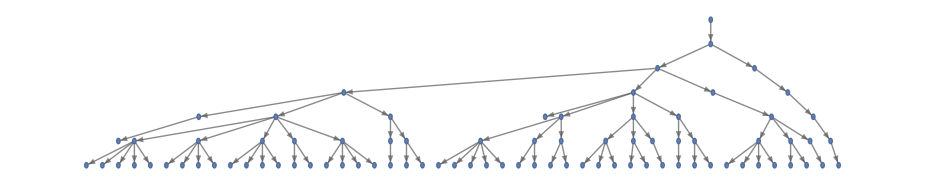

```mathematica
(* Stop evolution when a seen state is encountered *)
HGEvolve[rules, initialEdges, 6, "StatesGraphStructure", "EarlyTermination" -> True]
```

### Causal Transitive Reduction

```mathematica
(* Remove redundant causal edges *)
Print["With reduction: ", Length[HGEvolve[rules, initialEdges, 3, "CausalEdges", "CausalTransitiveReduction" -> True]]];
Print["Without reduction: ", Length[HGEvolve[rules, initialEdges, 3, "CausalEdges", "CausalTransitiveReduction" -> False]]]
```

With reduction: 52

Without reduction: 72

### Exploration Limits

Control the size of the multiway graph by limiting successors and states.

```mathematica
(* Limit number of successors per parent state *)
HGEvolve[rules, initialEdges, 5, "StatesGraphStructure", "MaxSuccessorStatesPerParent" -> 2]
```

-Graphics-

```mathematica
(* Limit total states at each step *)
HGEvolve[rules, initialEdges, 5, "StatesGraphStructure", "MaxStatesPerStep" -> 3]
```

-Graphics-

```mathematica
(* Probabilistic exploration (for sampling large spaces) *)
HGEvolve[rules, initialEdges, 8, "StatesGraphStructure", "ExplorationProbability" -> 0.25]
```

-Graphics-

### Graph Aspect Ratio

```mathematica
(* Control graph layout *)
HGEvolve[rules, initialEdges, 4, "StatesGraphStructure", "AspectRatio" -> 2/3]
```

-Graphics-

## Multiple Rules

Evolution can use multiple rewriting rules simultaneously.

```mathematica
(* Define multiple rules *)
multiRules = {
  {{1, 2, 3}} -> {{1, 2}, {2, 3}, {3, 1}},
  {{1, 2}} -> {{1, 3, 2}}
};

HGEvolve[multiRules, {{1, 2, 3}}, 3, "StatesGraph"]
```

-Graphics-

## Summary of Properties and Options

The HGEvolve function provides a comprehensive API for hypergraph rewriting.

### Available Properties

Data Properties:
- "States" - Association of state IDs to hypergraph edges
- "Events" - List of rewriting events
- "CausalEdges" - List of causal relationships between events
- "BranchialEdges" - List of branchial relationships between events

Count Properties:
- "NumStates" - Total number of states
- "NumEvents" - Total number of events
- "NumCausalEdges" - Total number of causal edges
- "NumBranchialEdges" - Total number of branchial edges
- "Debug" - Association with all counts at once

Graph Properties (with WolframModelPlot rendering):
- "StatesGraph" - Multiway graph of states
- "CausalGraph" - Causal graph of events
- "BranchialGraph" - Branchial graph of states
- "EvolutionGraph" - Combined states and events
- "EvolutionCausalGraph" - Evolution with causal edges
- "EvolutionBranchialGraph" - Evolution with branchial edges
- "EvolutionCausalBranchialGraph" - Full evolution (default)

Structure Properties (no rendering, for analysis):
- "StatesGraphStructure"
- "CausalGraphStructure"
- "BranchialGraphStructure"
- "EvolutionGraphStructure"
- "EvolutionCausalGraphStructure"
- "EvolutionBranchialGraphStructure"
- "EvolutionCausalBranchialGraphStructure"

### Available Options

"CanonicalizeStates" -> True/False (default: True)
  Identify isomorphic states and merge them

"CanonicalizeEvents" -> True/False (default: False)
  Identify duplicate events and count multiplicity

"CausalTransitiveReduction" -> True/False (default: True)
  Remove redundant causal edges

"EarlyTermination" -> True/False (default: False)
  Stop when encountering previously seen states

"AspectRatio" -> number or None (default: None)
  Control graph layout aspect ratio

"MaxSuccessorStatesPerParent" -> integer (default: 0 = unlimited)
  Limit number of successor states from each parent

"MaxStatesPerStep" -> integer (default: 0 = unlimited)
  Limit total number of states at each evolution step

"ExplorationProbability" -> 0.0 to 1.0 (default: 1.0 = always)
  Probability of exploring each potential branch